```mathematica
1+1
```

2

```mathematica
f[a_]:=omegam[a]^gamma[a]
```

```mathematica
omegam[a_]:=om/(a^3 e[a])
```

```mathematica
e[a_]:=Sqrt[om/a^3+(1-om)efe[a]]
```

```mathematica
gamma[a_]:=gamma0+gammap0(1/a-1)
```

```mathematica
f[2]
```

8^(-gamma0+gammap0/2) (om/(√(om/8+(1-om) efe[2])))^(gamma0-gammap0/2)

```mathematica
om=0.3;
gamma0=0.55;
gammap0=0.1;
```

```mathematica
s = NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a, 0.001, 0.99}]
```

NDSolve::mxst: Maximum number of 10000 steps reached at the point a == 0.156905.

{{efe→InterpolatingFunction[{{0.156905, 0.99}}, <>]}}

```mathematica
(*s = NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1-D[Log[omegam[a]], Log[a]])==(3omegam[a])/2, efe[1] == 1}, efe, {a, 0.001, 0.99}]*)
```

```mathematica
sol = efe/.Flatten[s];
```

InterpolatingFunction::dmval: Input value {0.0010202} lies outside the range of data in the interpolating function. Extrapolation will be used.

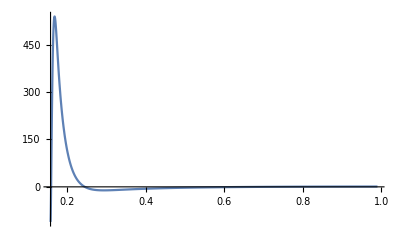

```mathematica
Plot[sol[a],{a,0.001,0.99}, PlotRange->All]
```